Инициализация...

Mathematica version is 10. Assigning RotationMatrix3D and BlockMatrix

Loading modules ...

Mathematica version is 10. Assigning OFULL via Join.

... completed.

==============================================

BM version: 6.02.001

Release date: 2016/04/12

Crystal Plate Reflection and Transmission. .

BerremanInitVersion = 6.02
BerremanCommonVersion = 6.02
BerremanDirectVersion = 6.02
BerremanInverseVersion = 5.03
FieldAlgebraVersion = 6.02
FieldIOVersion = 6.02
FieldIOFormatVersion = 6.02

Copyright: K^3, 2001 - 2016.

Email: konstantin.k.konstantinov@gmail.com

License type: GPL v3 or any later version, see http://www.gnu.org/licenses/

==============================================

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version. This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details. You should have received a copy of the GNU General Public License along with this program. If not, see http://www.gnu.org/licenses/ .

==============================================

Инициализация завершена.

==============================================

Параметры падающего света...

Upper refractive index n_u = 1, parameters: (200 | 1000 | 400 | λ | 1/1000000000
0 | 75 | 15 | ϕ | °
0 | 0 | 45 | β | °
0 | 0 | 0.5 | e | )

---------------------------------------------

Оптические параметры первого тонкого слоя.

epsLayer1 = (2.1316 | 0 | 0
0 | 2.1316 | 0
0 | 0 | 2.1316)

Оптические параметры нижней среды...

epsLower = (14.9766+0.12771 ⅈ | 0 | 0
0 | 14.9766+0.12771 ⅈ | 0
0 | 0 | 14.9766+0.12771 ⅈ)

Создаем оптическую систему...

---

Layered System = {LayeredSystem,{{1,3.87+0.0165 ⅈ,{0,0,30,γ,°},{{0,{{2.1316,0,0},{0,2.1316,0},{0,0,2.1316}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{2.1316,0,0},{0,2.1316,0},{0,0,2.1316}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},Layered System,1,0,{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{14.9766+0.12771 ⅈ,0,0},{0,14.9766+0.12771 ⅈ,0},{0,0,14.9766+0.12771 ⅈ}},{{1,0,0},{0,1,0},{0,0,1}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}}}},{{200,1000,400,λ,1/1000000000},{0,75,15,ϕ,°},{0,0,45,β,°},{0,0,30,γ,°},{0,0,0.5,e},{0,0,1,φ,°},{0,0,1,θ,°},{0,0,1,ψ,°},{0,0,30,φ_1,°},{0,0,30,θ_1,°},{0,0,30,ψ_1,°},{100,100,10,h,1/1000000000}},{UseThickLastLayer→False}}}

==============================================

Производим вычисления для различных значений параметров....

PerformAllCalculations::Calculating...

Start time: 15:18:27

Total number of points to calculate: 18

Estimated total calculation time: 0:00:00

Estimated end time: 15:18:27

==============================================

Using Optiva angles for rotation: 
Rotation 1: Fi (angle between crystal axis and deposition direction) - rotation around z; 
Rotation 2: Psi (angle between crystal axis and substrate plane.) - rotation around y (in the opposite direction!!!); 
Rotation 3: Alpha (rotation of crystal around its axis.) - rotation around x.

==============================================

==============================================

Printing Collection...

==============================================

*** Multilayered Thin Film Output File Format Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Modelling Engine Version 6.02 *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
* Description * |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
One Layer biaxial thin film between two semi-infinite media. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using Media Orientation Angles. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Solving for layered film between TWO SEMI-INFINITE isotropic media; nOut is IGNORED !!! |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Rotating all layers simultaneously. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  | Using consecutive rotations. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | AbsoluteAzimuth | Using Absolute Azimuth |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Options Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Refraction_Index |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1 |  | 3.87+0.0165 ⅈ |  | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Begin Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | Epsilon RE |  |  |  | Epsilon IM |  |  |  | Mu RE |  |  |  | Mu IM |  |  |  | Ro RE |  |  |  | Ro IM |  |  |  | RoT RE |  |  |  | RoT IM |  |  | 
 | 14.9766 | 0 | 0 |  | 0.12771 | 0 | 0 |  | 1 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 14.9766 | 0 |  | 0 | 0.12771 | 0 |  | 0 | 1 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
 | 0 | 0 | 14.9766 |  | 0 | 0 | 0.12771 |  | 0 | 0 | 1 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 |  | 0 | 0 | 0 | 
** End Detailed Substrate Block ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Thickness |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nothing to ouput so far... |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Media End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
n |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 1.46 | 0. | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 1.46 | 0. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0. | 0. | 1.46 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
k |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_RE |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 2.1316 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 2.1316 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 2.1316 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Epsilon_IM |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 0 | 0 | 0 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
** Film End ** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** End Optical Properties Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
*** Begin Output Block *** |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

(Input | No | λ | ϕ | β | γ | e | φ | θ | ψ | φ_1 | θ_1 | ψ_1 | h | Output | R | T | R_p | R_s | T_p | T_s
 | 1. | 200. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0895081 | 0.910492 | 0.0895081 | 0. | 0.910492 | 0.
 | 2. | 200. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0981199 | 0.90188 | 0.0981199 | 0. | 0.90188 | 0.
 | 3. | 200. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.129709 | 0.870291 | 0.129709 | 0. | 0.870291 | 0.
 | 4. | 200. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.160478 | 0.839522 | 0.160478 | 0. | 0.839522 | 0.
 | 5. | 200. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.127199 | 0.872801 | 0.127199 | 0. | 0.872801 | 0.
 | 6. | 200. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0485321 | 0.951468 | 0.0485321 | 0. | 0.951468 | 0.
 | 7. | 600. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0844975 | 0.915503 | 0.0844975 | 0. | 0.915503 | 0.
 | 8. | 600. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0866426 | 0.913357 | 0.0866426 | 0. | 0.913357 | 0.
 | 9. | 600. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.0958897 | 0.90411 | 0.0958897 | 0. | 0.90411 | 0.
 | 10. | 600. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.117579 | 0.882421 | 0.117579 | 0. | 0.882421 | 0.
 | 11. | 600. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.165208 | 0.834792 | 0.165208 | 0. | 0.834792 | 0.
 | 12. | 600. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.325508 | 0.674492 | 0.325508 | 0. | 0.674492 | 0.
 | 13. | 1000. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.2023 | 0.7977 | 0.2023 | 0. | 0.7977 | 0.
 | 14. | 1000. | 15. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.199868 | 0.800132 | 0.199868 | 0. | 0.800132 | 0.
 | 15. | 1000. | 30. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.190184 | 0.809816 | 0.190184 | 0. | 0.809816 | 0.
 | 16. | 1000. | 45. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.168147 | 0.831853 | 0.168147 | 0. | 0.831853 | 0.
 | 17. | 1000. | 60. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.138649 | 0.861351 | 0.138649 | 0. | 0.861351 | 0.
 | 18. | 1000. | 75. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100. |  | 0.190478 | 0.809522 | 0.190478 | 0. | 0.809522 | 0.)

*** End Output Block ***

Done.

==============================================

Saving Collection...

Done.

Sat 8 Oct 2016 15:18:28, time used: 1.802, total time used: 2.
---------------------------------------------

PerformAllCalculations::Plotting figures...

Full intensity of Reflected light.

-Graphics3D-

==============================================

Full intensity of Transmitted light.

-Graphics3D-

==============================================

Intensity of Reflected light going into X component.

-Graphics3D-

==============================================

Intensity of Reflected light going into Y component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into X component.

-Graphics3D-

==============================================

Intensity of Transmitted light going into Y component.

-Graphics3D-

==============================================

Full intensity of Reflected light.

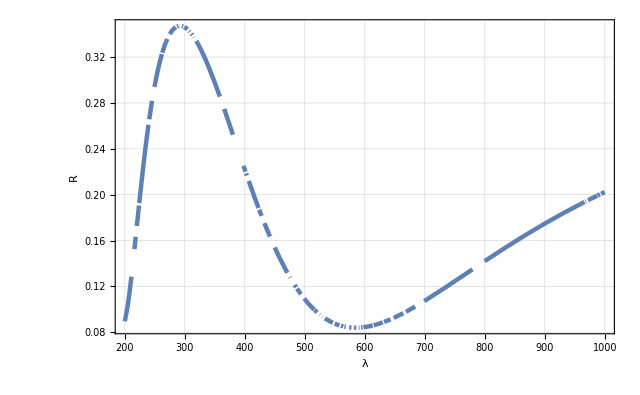

Full intensity of Transmitted light.

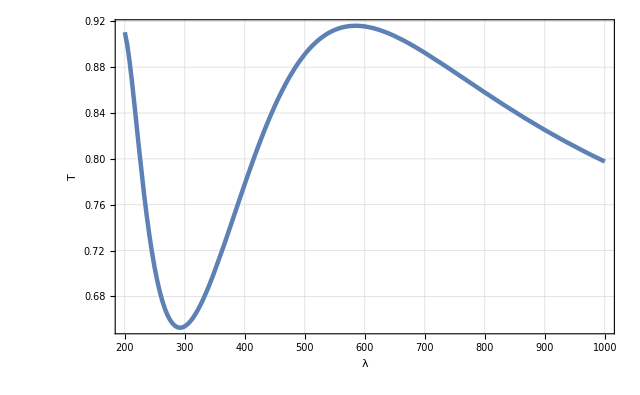

{Intensity of Reflected light going into X component.,Intensity of Reflected light going into Y component.}

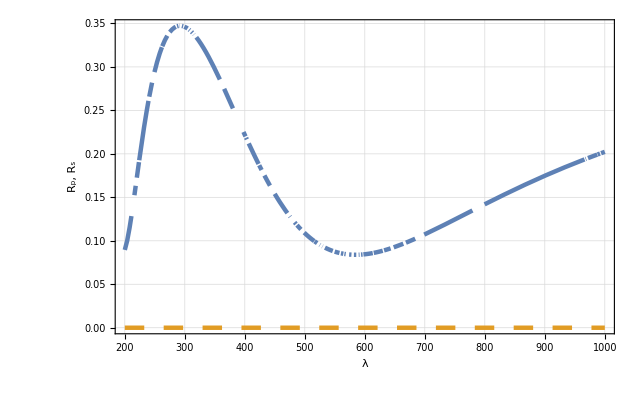

{Intensity of Transmitted light going into X component.,Intensity of Transmitted light going into Y component.}

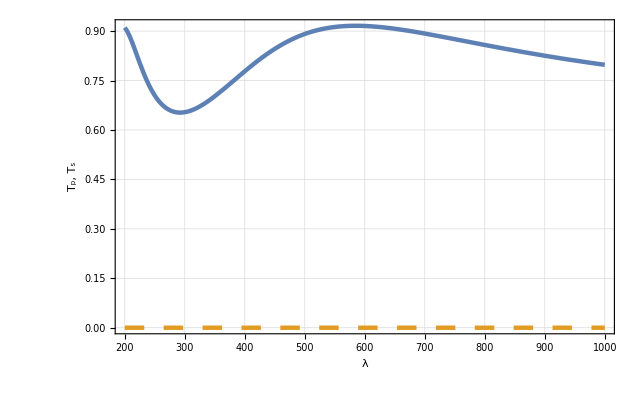

Sat 8 Oct 2016 15:19:23, time used: 55.036, total time used: 57.
---------------------------------------------

```mathematica
(* ============================================== *)
ClearAll["Global`*"];
(* ============================================== *)
PathList={"W:\\Math\\BM\\"};
BaseDir="W:\\Math\\BM\\";
BaseFileName="Example_06";
OutDir=BaseDir<>"Calc\\";
(* ============================================== *)
useParallelTbl=False;
Get["BerremanInit.m",Path-> PathList];
Initialize[PathList, useParallelTbl];
(* ============================================== *)
opts={BDPlotFigures -> True,UseEulerAngles->False};
(* ============================================== *)
(*
FuncList={{StokesVectorI[1],StokesVectorI[2],StokesVectorI[3],StokesVectorI[4]},{StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4]},{EltEG[1],EltEG[2],EltEG[3],EltEG[4]},{XitEGDegree[1],XitEGDegree[2],XitEGDegree[3],XitEGDegree[4]},{IFull,RFull,TFull},{Ix,Iy,Rx,Ry,Tx,Ty},{Eli,Elr,Elt},{XiiDegree, XirDegree,XitDegree},{Sin2Xii,Sin2Xir,Sin2Xit}};
*)
(*
FuncList={StokesVectorR[1],StokesVectorR[2],StokesVectorR[3],StokesVectorR[4],RFull,TFull, StokesGammaR, StokesGammaDegreeR,StokesChiR, StokesChiDegreeR, StokesPolarizedR,XirDegree,Elr,PsiPPDegree,DeltaPPDegree,{Rx,Ry},{Tx,Ty}};
*)
FuncList={RFull,TFull,{Rx,Ry},{Tx,Ty}};

(* ============================================== *)
systemDescription="One Layer biaxial thin film between two semi-infinite media.";
(* ============================================== *)
Print["Параметры падающего света..."];
nUpper=1; 

lambda={200,1000,400,"λ",nm};fita={0,75,15,"ϕ", Degree};beta={0,0,45,"β", Degree};gamma={0, 0,30,"γ",Degree};
ellipt={0,0,0.5,"e"};

incidentLight=CreateIncidentRay[nUpper,lambda,fita,beta, ellipt];
OutputIncidentRayInfo[incidentLight];
(* ============================================== *)
Print["Оптические параметры первого тонкого слоя."];
fiLayer1={0, 0, 30,Subscript["φ","1"], Degree};thetaLayer1={0,0,30,Subscript["θ","1"],Degree};psiLayer1={0,0,30,Subscript["ψ","1"], Degree};
rotationAnglesLayer1={fiLayer1,thetaLayer1,psiLayer1};

thicknessLayer1={100,100,10,"h",nm};

epsLayer1=EpsilonFromN[1.46];
Print["epsLayer1 = ", epsLayer1 // MatrixForm];

layer1=CreateFilm[thicknessLayer1,rotationAnglesLayer1,epsLayer1];
(* ============================================== *)
Print["Оптические параметры нижней среды..."];
fi={0,0,1,"φ", Degree};
theta={0,0,1,"θ", Degree};
psi={0,0,1,"ψ", Degree};
rotationAngles={fi,theta,psi};
(*
nLower=1.5;
lowerMedia=CreateSemiInfiniteMediaFromN[nLower];
*)
epsLower=EpsilonFromN[3.87+I*0.0165];
Print["epsLower = ", epsLower // MatrixForm];

(*
muLower=DiagonalMatrix[{1,1,1}];
rhoLower=I*DiagonalMatrix[{0,0,0}];
Print["muLower = ", muLower // MatrixForm];
Print["rhoLower = ", rhoLower // MatrixForm];
*)
(* lowerMedia=CreateSemiInfiniteMedia[rotationAngles,epsLower,muLower,rhoLower];  *)
lowerMedia=CreateSemiInfiniteMedia[rotationAngles,epsLower];
(* Print ["lowerMedia = ", lowerMedia]; *)
(* ============================================== *)
Print["Создаем оптическую систему..."];
layeredSystem = CreateLayeredSystem[incidentLight,gamma,layer1,lowerMedia];
OutputLayeredSystem[layeredSystem];
(* ============================================== *)
Print["Производим вычисления для различных значений параметров...."];
allCalc=PerformAllCalculations[layeredSystem,FuncList, systemDescription,opts];
(* ============================================== *)
```